```mathematica
(*The following clear command will make sure that any previous definitions of x no longer apply*)
```

```mathematica
Clear[x]
```

```mathematica
(*The command NIntegrate will allow us to find a numerical approximation of the integrating factor. If we have the equation x'+px=t 
with initial condition x(0)=3, and if p(t)=1/(1+Sqrt[t]), then we can find the integrating factor as follows: *)
```

```mathematica
u[s_]:=Exp[ NIntegrate[1/(1+Sqrt[z]),{z,0,s}]];
```

```mathematica
(*The full solution will then be found by using our formula:*)
```

NIntegrate::nlim: z = s is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
x[t_]:=3/u[t]+ (1/u[t])NIntegrate[u[s]s,{s,0,t}];
```

NIntegrate::nlim: z = s is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

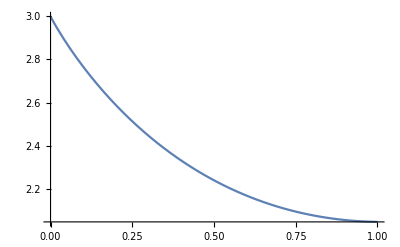

```mathematica
Plot[x[t],{t,0,1}]
```

```mathematica
(*We can use NDsolve to have the computer give its own numerical approximation. Since x[t] is already defined, then we use Module to use the variable locally *)
```

NIntegrate::nlim: z = s is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

```mathematica
v=NDSolve[{y'[t]==-1/(1+Sqrt[t])y[t]+t,y[0]==3},y,{t,0,1}];
```

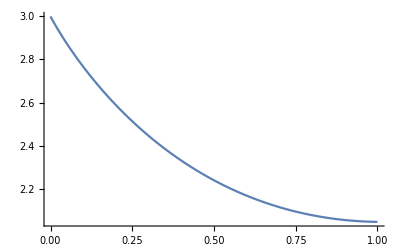

```mathematica
Plot[Evaluate[y[t]/.v],{t,0,1},PlotRange->All]
```

```mathematica
(*Notice how much faster using NDsolve can be. We will discuss later how the computer estimates. *)
```

```mathematica
(*We now look at solving the same equation, but this time using Picard iteration*)
```

```mathematica
Clear[x,t,s];

x[1,t_]:=3+NIntegrate[-1/(1+Sqrt[s])3+s,{s,0,t}];
```

```mathematica
(*We use Module to make s a local variable*)
```

```mathematica
x[2,t_]:=3+Module[{s},NIntegrate[-1/(1+Sqrt[s])x[1,s]+s,{s,0,t}]];
```

NIntegrate::nlim: s = s$2343046 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

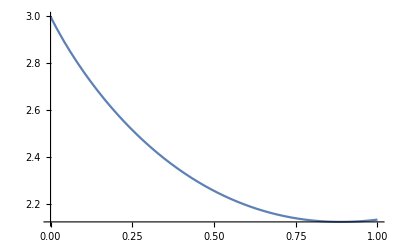

```mathematica
Plot[x[2,t],{t,0,1}]
```

```mathematica
(*Finally, let us clear the variables and consider a nontrivial problem
x'=cos(x+t) with zero initial condition*)
Clear[x,t,s,y];
```

```mathematica
x[1,t_]=NIntegrate[Cos[0+s],{s,0,t}];
```

NIntegrate::nlim: s = t is not a valid limit of integration.

```mathematica
x[2,t_]=Module[{s},NIntegrate[Cos[x[1,s]+s],{s,0,t}]];
```

NIntegrate::nlim: s = t is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::nlim: s = s$8062544 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

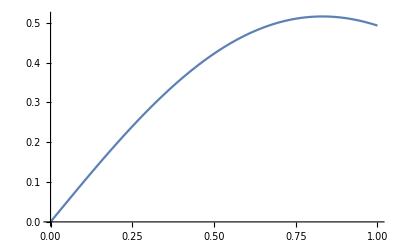

```mathematica
Plot[x[2,t],{t,0,1}]
```

```mathematica
w=NDSolve[{y'[t]==Cos[y[t]+t],y[0]==0},y,{t,0,1}];
```

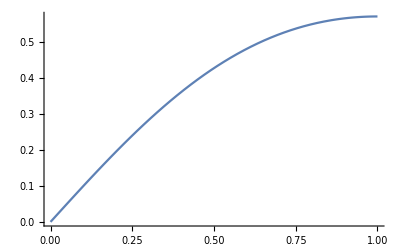

```mathematica
Plot[Evaluate[y[t]/.w],{t,0,1},PlotRange->All]
```

```mathematica
(*Notice we can actually solve x[1,t] by hand*)
```